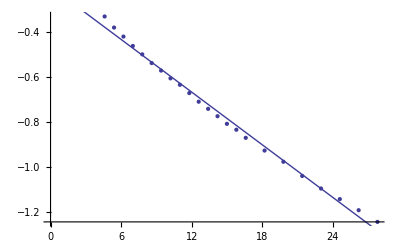

```mathematica
data2 = {{2.3, 7.48},{2.7,7.12},{3.1,6.84},{3.5,6.56},{3.9,6.32},{4.3,6.08},{4.7,5.88},{5.1, 5.68},{5.5, 5.52},{5.9,5.32},{6.3,5.12},{6.7,4.96},{7.1,4.8},{7.5,4.64},{7.9,4.52},{8.3,4.36},{9.1, 4.12},{9.9,3.92},{10.7,3.68},{11.5,3.48},{12.3,3.32},{13.1,3.16},{13.9,3}};
For[
i=1,
i<24,
i++,
data2[[i,1]] = 2*data2[[i,1]];
data2[[i,2]] = Log[data2[[i,2]]/10.4]
]
data2plot = ListPlot[data2];
lm2 = LinearModelFit[data2,x,x];
model2plot = Plot[lm2[x],{x,0,30}];
Show[data2plot,model2plot]
```

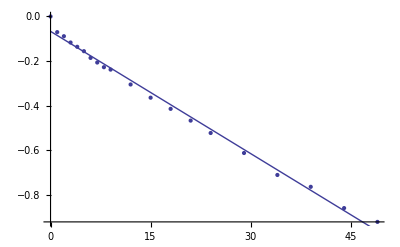

```mathematica
data1 = {{0,0},{1,.64},{2,.8},{3,1.04},{4,1.2},{5,1.36},{6,1.6},{7,1.76},{8,1.92},{9,2},{12,2.48},{15,2.88},{18,3.2},{21,3.52},{24,3.84},{29,4.32},{34,4.8},{39,5.04},{44,5.44},{49,5.68}};
For[
i = 1,
i<21,
i++,
data1[[i,2]]=Log[1-data1[[i,2]]/9.44]
]
data1plot = ListPlot[data1];
lm1 = LinearModelFit[data1,x,x];
model1plot = Plot[lm1[x],{x,0,50}];
Show[data1plot,model1plot]
```

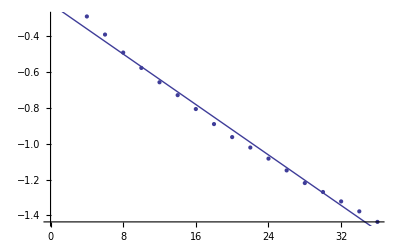

```mathematica
(*Redo times for T2 Petroleum Jelly*)
data3 = {{2,8.32},{3,7.52},{4,6.8},{5,6.24},{6,5.76},{7,5.36},{8,4.96},{9,4.56},{10,4.24},{11,4},{12,3.76},{13,3.52},{14,3.28},{15,3.12},{16,2.96},{17,2.8},{18,2.64}};
For[
i=1,
i<18,
i++,
data3[[i,1]] = 2*data3[[i,1]];
data3[[i,2]] = Log[data3[[i,2]]/11.1]
]
data3plot = ListPlot[data3];
lm3 = LinearModelFit[data3,x,x];
model3plot = Plot[lm3[x],{x,0,40}];
Show[data3plot,model3plot]
```